```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataLocal=Import["data-local-kris.txt","Table"];
dataRemote=Import["data-remote-kris.txt","Table"];
```

```mathematica
extractData[{{"------------------------------------"},{__,numThreads_},{__,throughput_},{__,latency_},{__,successfulRatio_},{__,customerRatio_},{__,successfulCustomerRatio_},{"------------------------------------"},rs__}]:=
Prepend[extractData[{rs}],{numThreads,throughput,latency,successfulRatio,customerRatio,successfulCustomerRatio}];
extractData[{{___},rs___}]:=extractData[{rs}];
extractData[{}]:={};
```

```mathematica
extractedLocal=extractData[dataLocal][[1;;14]];
extractedRemote=extractData[dataRemote];
```

```mathematica
({#[[1]],#[[2]]}&/@#&)/@{extractedLocal,extractedRemote}
```

{{{1,4.07256},{2,19.8631},{3,25.9527},{4,14.9417},{5,22.8872},{6,19.041},{7,17.7921},{8,15.9674},{9,13.4388},{10,10.7756},{11,11.6037},{12,10.8086},{13,10.3547},{14,9.40275}},{{1,0.03991},{2,0.084973},{3,0.114872},{4,0.108918},{5,0.105599},{6,0.085791},{7,0.074973},{8,0.060852},{9,0.069054},{10,0.082607},{11,0.067117},{12,0.062341},{13,0.053934},{14,0.054204}}}

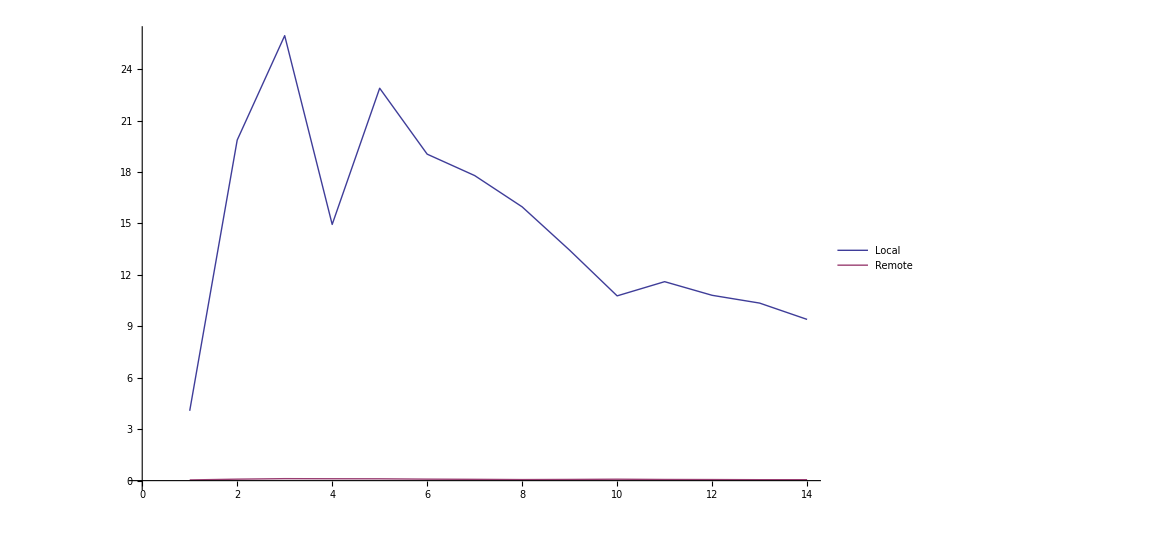

```mathematica
throughputGraph=ListLinePlot[({#[[1]],#[[2]]}&/@#&)/@{extractedLocal,extractedRemote},PlotLegends->{"Local","Remote"}]
```

```mathematica
Export["throughput-combined-kris.pdf", throughputGraph];
```

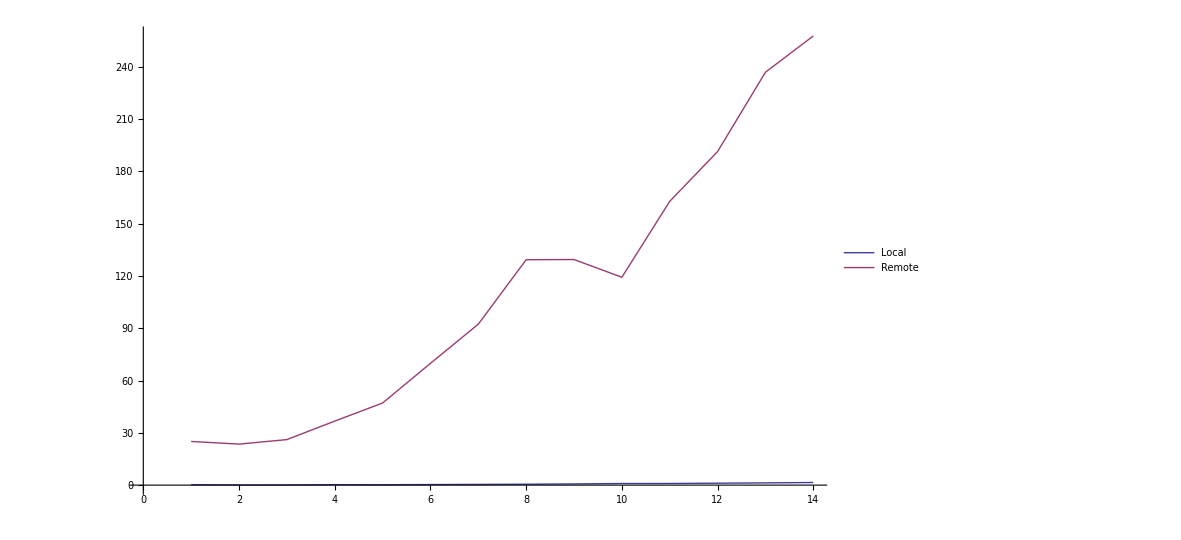

```mathematica
latencyGraph=ListLinePlot[({#[[1]],#[[3]]}&/@#&)/@{extractedLocal,extractedRemote},PlotLegends->{"Local","Remote"}]
```

```mathematica
Export["latency-combined-kris.pdf", latencyGraph];
```

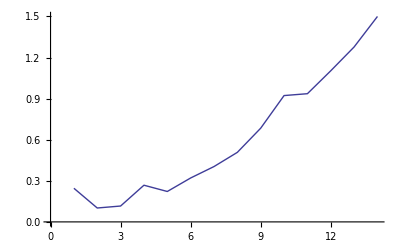

```mathematica
latencyGraph=ListLinePlot[{#[[1]],#[[3]]}&/@extractedLocal]
Export["latency-local-kris.pdf",latencyGraph];
```